```mathematica
symbols = FinancialData[]
```

```mathematica
gg="NASDAQ:GOOG"
```

NASDAQ:GOOG

```mathematica
MemberQ[symbols,gg]
```

True

```mathematica
timeseries=FinancialData[gg,{"2020-01-01","2024-41-01"}]
```

TimeSeries[…]

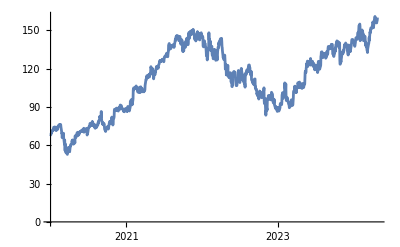

```mathematica
ListPlot[timeseries,{Joined->True}]
```

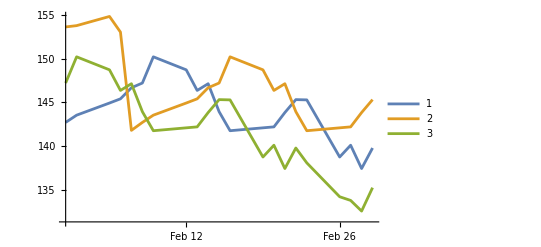

```mathematica
ListPlot[
{TimeSeriesWindow[ts1,dd],
TimeSeriesWindow[TimeSeriesShift[ts1,{7,"Day"}],dd],
TimeSeriesWindow[TimeSeriesShift[ts1,{-7,"Day"}],dd]
},{Joined->True,PlotLegends->True}]
```

```mathematica
ts1=FinancialData["NASDAQ:GOOG",{"2023-01-01","2024-04-01"}]
ts2=FinancialData["NASDAQ:AAPL",{"2023-01-01","2024-04-01"}]
```

TimeSeries[…]

TimeSeries[…]

```mathematica
CheckPredictionPower[target_,predictor_,shiftDays_:7]:=Correlation[target,TimeSeriesShift[predictor,{-shiftDays,"Day"}]]
```

```mathematica
CheckPredictionPower[ts1, ts2]
```

0.047951

```mathematica
Correlation[ts1,ts2]
```

0.047951

```mathematica
CheckPredictionPower[ts1, ts1]
```

1.

```mathematica
ts1
```

TimeSeries[…]

```mathematica
tt=TimeSeriesShift[ts1,{-7,"Day"}]
```

TimeSeries[…]

```mathematica
Correlation[ts1,tt]
```

1.

```mathematica
CheckCorrelation[target_,predictor_,window_,shiftDays_:7]:=
Correlation[
TimeSeriesWindow[target,window],
TimeSeriesWindow[TimeSeriesShift[predictor,{shiftDays,"Day"}],window]]
```

```mathematica
CheckCorrelation[ts1,ts1,DateObject[{2024,2},"Month"],14]
```

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Correlation[TimeSeries[…],TimeSeries[…]]

```mathematica
dd=DateObject[{2024,2},"Month"]
```

Feb 2024

```mathematica
CheckCorrelation[ts1,ts1,DateObject[{2024,2},"Month"],-7]
```

0.604042

```mathematica
CheckCorrelation[ts1,ts2,DateObject[{2024,2},"Month"],7]
```

0.321983